## 22.S09 – Molten Salt Brick Heat Transfer Model

## 2) basic heat loss from brick (heat flow in Q) using 240,000 KJ/day of coal rn energy density of molten salt brick how long would the salt take to solidify? 3) volume of molten salt necessary given heat loss (heat flow Q is in W) (heat capacity up to melting temperature (see p.803), then some way of modelling phase change?, then heat capacity once solidified) 4) need model for temperature within the ger at a given the temperature of the brick (this should somehow incorporate phase change?) (George’s pset might be a good reference)

#### Setting initial variables for our brick in tent system.

#### Assumptions: - ger and the molten salt brick are shaped like cubes - all dimensions are in SI units - no forced convection - resistance in stainless steel around molten brick is negligible -salt is mix of NaNO3 & KNO3

```mathematica
N[(240000/(1840*(2660*(773-495)+120+2660*(495-300))))*10^6]
```

103.66

```mathematica
gerw = 5; (*need to update*)
gerl = 5;(*need to update*)
gerh = 5;(*need to update*)
brickw = 0.1;(*need to update*)
brickl = 0.1;(*need to update*)
brickh= 0.1;(*need to update*)
hair = 10;
ksalt = 1; (*need to look up actual value*)
cpmoltensalt = 1500; (*does cp differ for solid salt?*)
densitysalt = 2200;
Tmsalt = 494;
hfsalt = 1; (*need actual value*)
Tibrick = 873;
(*Tbrick = 300; (*make this a function of time*)*)
Titent = 290;
σ = 5.67*10^(-8);
ϵsteel = 0.7;
krockwool = .035; (*verify this*)
ϵinsulation = 0.95;
(*this is an educated guess*)
```

#### Which forms of heat transfer dominate? Checking at lowest ΔT because heat flux via radiation tends to dominate at higher temperatures

```mathematica
Rradiative[σ_,ϵ_,Tsurf_, Tsource_] := 1/(σ ϵ (Tsurf^2+Tsource^2)(Tsurf+Tsource))
```

```mathematica
Rconvective[h_] := 1/h
```

```mathematica
Rradbrick = Rradiative[σ,ϵsteel, Tbrick,Titent]
Rconvbrick = Rconvective[hair]
```

0.245283

1/10

#### Even at lowest ΔT, radiative and convective resistance terms are within an order of magnitude of each other. Therefore, both radiation and convection must be considered in our heat transfer model.

#### Insulation around the molten brick

#### Begin by assuming steady state Heat balance at interface between insulation and air: q_convection+q_radiation = q_conduction R_conduction= L/k h (T_surface - T_fluid) + ϵ σ (T_surface^4- T_source^4) = ΔT/R

```mathematica
Rconductive[L_,k_] := L/k;
qradiative[ϵ_,Tsurface_,Tsource_]:=ϵ σ (Tsurface^4-Tsource^4);
qconvective[h_,Tsurface_,Tfluid_]:= h (Tsurface-Tfluid);
qconductive[R_,Tinitial_,Tfinal_]:= (Tfinal-Tinitial)/R;
```

```mathematica
Rcondinsul = Rconductive[L,krockwool];
qradinsul =qradiative[ϵinsulation,Tsurf,Titent];
qconvinsul = qconvective[hair,Tsurf,Titent];
qcondinsul = qconductive[Rcondinsul,Tsurf,Tbricktime];
```

```mathematica
Solve[qconvinsul+qradinsul==qcondinsul,Tbricktime]
```

{{Tbricktime→-28.5714 L (-10. (-290.+Tsurf)-(0.035 Tsurf)/L-5.3865×10^-8 (-7.07281×10^9+Tsurf^4))}}

```mathematica
bricktemp = -28.57142857142857 L (-10. (-290.+Tsurf)-(0.035 Tsurf)/L-5.386499999999999*^-8 (-7.07281*^9+Tsurf^4));
```

#### Assuming 50°C as a comfortable surface temperature on the outside of the insulation, what thickness of insulation is needed at various molten salt brick temperatures?

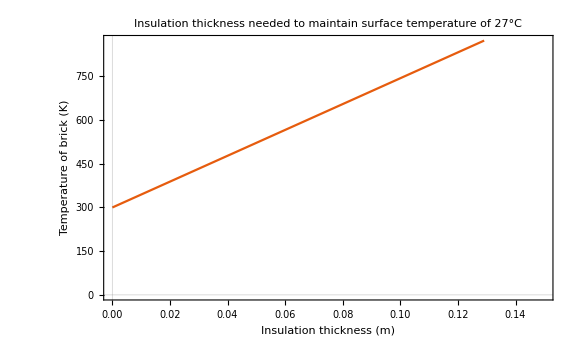

```mathematica
Plot[ bricktemp /. {Tsurf -> 300},{L,0,0.15},ImageSize->Large,PlotTheme -> "Scientific",FrameLabel->{Style["Insulation thickness (m)",14,Black],Style["Temperature of brick (K)",14,Black]},PlotLabel -> Style["Insulation thickness needed to maintain surface temperature of 27°C",16,Black,Bold],PlotRange->{0,873} ]
```

#### Heat loss from brick.

#### Volume of molten salt needed given heat loss.

#### Temperature profile for brick surface temperature over time. Neglecting phase transition for now.

#### Set up heat balance.

#### Heat balance: Q_accumulated = Q_in + Q_out + Q_generated Cross-sectional area remains constant: q_accumulated = q_in + q_out + q_generated q_accumulated = ρ c_p δT/δt q_in = - k∇T q_out = q_convective + q_radiative = h (T_surface - T_fluid) + ϵ σ (T_surface^4- T_source^4) q_generated = 0 ρ c_p δT/δt = -k(δT/δx+δT/δy+δT/δz) - (h (T_surface - T_fluid) + ϵ σ (T_surface^4- T_source^4))

#### Set initial and boundary conditions.

#### Insulation calculation @x=L, q_cond=q_conv

#### s = 2 sqrt[(k/rho*cp) t] 11in

```mathematica
Solve[ssalt == 2 Sqrt[ksalt/(densitysalt*cpmoltensalt) t],t]/.ssalt-> .0635
```

{{t→3326.61}}

```mathematica
t/.{{t->3326.6062500000003}}
```

{3326.61}

```mathematica
3326./3600.
```

0.923889